## V2: Now I also have wave function renormalization NO THE β-FUNCTION IS JUST dg/dμ!!!

```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
FS=FullSimplify;
```

# βFunction[]

## βFunction[] Definition

```mathematica
ClearAll[βFunction];

Options[βFunction]={"print"->False};

βFunction[coupling_,OptionsPattern[]]:=Module[{gr,βf,nLoop,i},
Clear[g,g0,μ,ϵ];

gr=coupling;
nLoop=Exponent[coupling,g0];
If[OptionValue["print"],
Print["Initial effective couling:\n ",gr,"\n"];];

βf=-μ D[gr,μ]//Expand;
If[OptionValue["print"],
Print["\nβ-function with bare coupling: ", βf,"\n"];];

gr=g-coupling+g0 μ^-ϵ;

If[OptionValue["print"],
Print[" Bare coupling= \n ",gr,"\n"];];

Do[βf=βf/.g0^n_ μ^(-n_ ϵ):>(gr)^n μ^(n ϵ)//Expand;
βf=βf/.(g0 ):>(gr)μ^ϵ//Expand;
(*βf=Series[βf,{g0,0,nLoop}]//Expand;*)
βf=βf/.g0^n_/;n>nLoop:>0;
βf=βf/.g0^n_/;n==nLoop:>(g μ^ϵ)^n//Expand;
If[OptionValue["print"],
Print[βf//FullSimplify,"\n"];];
,{i,1,nLoop}];

(*For[i=1,i<=nLoop,i++,
βf=βf/.g0^n_ μ^(n_ ϵ):>(gr)^n//Expand;
βf=βf/.(g0 μ^ϵ):>(gr)//Expand;
];*)

βf=Normal[βf]/.g0^n_ :>(g μ^ϵ)^n//Expand;
βf=βf/.(g0 ):>(g μ^ϵ)//Expand;
βf=Series[βf,{g,0,nLoop}]//Expand;
(*Print[βf];*)
(*βf=Normal[βf];*)
Return[βf//FullSimplify]]
```

## Tests and Results

### §LRW (No wave-function renormalization)

#### Coupling: 1-Loop (OK)

```mathematica
g=g0 μ^-ϵ-a banana (g0 μ^-ϵ)^2;
βFunction[g,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)//FullSimplify;
Collect[%,{1/ϵ}];
RGeq1=(%//FullSimplify)/g==0//FullSimplify
```

ϵ g-a banana ϵ g^2+O[g]^3

a g==ϵ

```mathematica
gc1=g/.Flatten@Solve[RGeq1,g]
```

ϵ/a

#### Coupling: 2-Loop (OK)

```mathematica
g=g0 μ^-ϵ-a banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3(A doubleBanana + B hat);
βFunction[g,1,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)//FullSimplify;
Collect[%,{1/ϵ}]
RGeq2=(%/.Flatten@Solve[-2 a^2+2 A+B==0,A]//FullSimplify)/g==0//FullSimplify
```

ϵ g-a banana ϵ g^2+(-2 a^2 banana^2 ϵ+2 A doubleBanana ϵ+2 B hat ϵ) g^3+O[g]^4

-a g^2+(B g^3)/2+((-2 a^2+2 A+B) g^3)/ϵ+g ϵ

2 a g==B g^2+2 ϵ

To remove divergences we need

```mathematica
Flatten@Solve[-2 a^2+2 A+B==0,A]//Simplify
```

{A→a^2-B/2}

Let’s get the 2-Loop critical g

```mathematica
gc2=gc1+b ϵ^2
RGeq2/.g->gc2;
Expand[%]/.ϵ^n_/;n>2:>0;
gc2=gc2/.Flatten@Solve[%,b]
```

ϵ/a+b ϵ^2

ϵ/a+(B ϵ^2)/(2 a^3)

### §With wave-function renormalization

#### Coupling: 1-Loop (OK!!)

```mathematica
g=g0 μ^-ϵ-2 banana (g0 μ^-ϵ)^2;
Zϕ=1+banana g0 μ^-ϵ;
βFunction[g /Zϕ,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)//FullSimplify;
Collect[%,{1/ϵ}];
RGeq1=(%//FullSimplify)/g==0//FullSimplify
```

ϵ g-3 (banana ϵ) g^2+O[g]^3

3 g==ϵ

```mathematica
gc1=g/.Flatten@Solve[RGeq1,g]
```

ϵ/3

#### Coupling: 2-Loop (OK??)

```mathematica
g=g0 μ^ϵ-a banana (g0 μ^ϵ)^2+(g0 μ^ϵ)^3(A doubleBanana + B hat);
βFunction[g,1]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)//FullSimplify;
Collect[%,{1/ϵ}]
RGeq2=(%/.Flatten@Solve[-2 a^2+2 A+B==0,A]//FullSimplify)/g==0//FullSimplify
```

ϵ g-a banana ϵ g^2+(-2 a^2 banana^2 ϵ+2 A doubleBanana ϵ+2 B hat ϵ) g^3+O[g]^4

-a g^2+(B g^3)/2+((-2 a^2+2 A+B) g^3)/ϵ+g ϵ

2 a g==B g^2+2 ϵ

To remove divergences we need

```mathematica
Flatten@Solve[-2 a^2+2 A+B==0,A]//Simplify
```

{A→a^2-B/2}

Let’s get the 2-Loop critical g

```mathematica
gc2=gc1+b ϵ^2
RGeq2/.g->gc2;
Expand[%]/.ϵ^n_/;n>2:>0;
gc2=gc2/.Flatten@Solve[%,b]
```

ϵ/a+b ϵ^2

ϵ/a+(B ϵ^2)/(2 a^3)

### § b-LRW 2-loop:

#### Using my result

```mathematica
g=g0 μ^-ϵ-(b+2)banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3 (b+2)( doubleBanana + 2(b+1) hat);
βFunction[g,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)//FullSimplify
RGeq2=Normal[%]==0;
```

ϵ g-(2+b) banana ϵ g^2-2 ((2+b) ((2+b) banana^2-doubleBanana-2 (1+b) hat) ϵ) g^3+O[g]^4

ϵ g+(-2-b) g^2+(1+b) (2+b) g^3+O[g]^4

```mathematica
(*Nice, this is finite*)
```

Let’s check Kay’s ansatz for g (from his email “picture”): OK, IT IS FINITE TOO

```mathematica
g=g0 μ^-ϵ-(b+2)banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3 ( (b^2+2)doubleBanana + 4(2b+1) hat );
βFunction[g,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)//FullSimplify
RGeq2=Normal[%]==0;
```

ϵ g-(2+b) banana ϵ g^2+2 (-(2+b)^2 banana^2+(2+b^2) doubleBanana+4 hat+8 b hat) ϵ g^3+O[g]^4

ϵ g+(-2-b) g^2+(2+4 b) g^3+O[g]^4

Let’s get the 2-Loop critical g

```mathematica
gc1=ϵ/(b+2);
gc2=gc1+A ϵ^2
RGeq2/.g->gc2;
Expand[%];
%/.ϵ^n_/;n>3:>0;
gc2=Collect[gc2/.Flatten@Solve[%,A]//FullSimplify,{ϵ,ϵ^2},FullSimplify]
```

ϵ/(2+b)+A ϵ^2

ϵ/(2+b)+((1+b) ϵ^2)/(2+b)^2

```mathematica
(*OK*)
```

#### Using my result EXTENDED WITH WAVE-FUNCTION RENORMALIZATION

```mathematica
g=g0 μ^-ϵ-(b+2)banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3( (b+2)( doubleBanana + 2(b+1) hat)-a b(b-1)1/2 sunset);
βFunction[g,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor
RGeq2=Normal[%]==0;
```

ϵ g-(2+b) banana ϵ g^2+(-2 (2+b)^2 banana^2+2 (2+b) (doubleBanana+2 (1+b) hat)-a (-1+b) b sunset) ϵ g^3+O[g]^4

ϵ g+(-2-b) g^2+(2+1/8 a (-1+b) b+b (3+b)) g^3+O[g]^4

```mathematica
(*Nice, this is finite*)
```

# γFunction[]

## γFunction[] Definition

```mathematica
ClearAll[γFunction];


Options[γFunction]={"print"->False};


γFunction[observable_,bareCoupling_, OptionsPattern[]]:=Module[{U,gr,γf,nLoop,i},
Clear[g,g0,μ,ϵ];
U=observable;
gr=bareCoupling;
nLoop=Exponent[gr,g0]-1;
(*Print[nLoop]*);

γf=-μ D[Log[U],μ]//Expand;
If[OptionValue["print"],
Print[" γf(g_0)= \n ",γf];];


gr=g-gr+g0 μ^-ϵ;

If[OptionValue["print"],
Print[" Bare coupling= \n ",gr];];

Do[γf=γf/.g0^n_ :>(gr)^n μ^(n ϵ)//Expand;
γf=γf/.(g0 ):>(gr)μ^ϵ//Expand;
γf=γf/.g0^n_/;n>nLoop:>0;
γf=γf/.g0^n_/;n==nLoop:>(g μ^ϵ)^n//Expand;
,{i,1,nLoop}];

(*For[i=1,i<=nLoop,i++,
γf=γf/.g0^n_ μ^(n_ ϵ):>(gr)^n//Expand;
γf=γf/.(g0 μ^ϵ):>(gr)//Expand;
];*)

γf=γf/.g0^n_ :>(g)^n μ^(n ϵ)//Expand;
γf=γf/.(g0 ):>(g)μ^ϵ//Expand;
(*
If[OptionValue["print"],
Print[" γf(g)= \n ",γf];];*)

γf=Series[γf,{g,0,nLoop}]//Expand;
γf=Factor@Simplify/@γf;
(*Print[γf];*)
(*γf=Normal[γf];*)
Return[γf]]
```

## Results LRW

### § U observable: 1-Loop (OK)

```mathematica
g=g0 μ^-ϵ-a banana (g0 μ^-ϵ)^2;
U=1-au g0 μ^-ϵ banana +(g0 μ^-ϵ)^2(A doubleBanana + B hat);
γFunction[U,g];
%/.banana->1/ϵ//FullSimplify
Normal[%]/.g->gc1
```

-au g+O[g]^2

-(au ϵ)/a

To get the correct ϵ correction we need

```mathematica
Flatten@Solve[au/a==1/3]
```

{au→a/3}

### U observable: 2-Loop (OK)

Generic values

```mathematica
g=g0 μ^-ϵ-a banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3(A doubleBanana + B hat);
U=1-au g0 μ^-ϵ banana +(g0 μ^-ϵ)^2(Au doubleBanana + Bu hat);
γFunction[U,g];
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)//FullSimplify;
%/.{au->a/3}//FullSimplify;
Collect[%,{1/ϵ,g^2}]
2+(%/.Au->(2 a^2)/9-Bu/2)/.g->gc2//Expand;
Z=Collect[%/.ϵ^n_/;n>2:>0,ϵ^2,Simplify]
```

-(a g)/3+(Bu g^2)/2+((-(4 a^2)/9+2 Au+Bu) g^2)/ϵ

2-ϵ/3-((B-3 Bu) ϵ^2)/(6 a^2)

To remove divergences we need

```mathematica
Flatten@Solve[-(4 a^2)/9+2 Au+Bu==0,Au]//Simplify
```

{Au→(2 a^2)/9-Bu/2}

To get the correct ϵ^2 correction we need

```mathematica
Flatten@Solve[(B-3 Bu)/(6 a^2)==1/9,B]//Simplify
```

{B→(2 a^2)/3+3 Bu}

Fixed values: {a -> 3, au -> 1, A -> 3, B -> 12, Au -> 1, Bu -> 2}

```mathematica
g=g0 μ^-ϵ-a banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3(A doubleBanana + B hat);
U=1-au g0 μ^-ϵ banana +(g0 μ^-ϵ)^2(Au doubleBanana + Bu hat);
γFunction[U,g];
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)//FullSimplify;
Collect[%,{1/ϵ,g^2}]
2+(%)/.g->gc2/.{a->3,au->1,A->3,B->12,Au->1,Bu->2}//Expand;
Z=Collect[%/.ϵ^n_/;n>2:>0,ϵ^2,Simplify]
```

-au g+(Bu g^2)/2+((-au (a+au)+2 Au+Bu) g^2)/ϵ

2-ϵ/3-ϵ^2/9

```mathematica
(* CORRECT *)
```

### γ vertex: 2-Loop with two bananas

Fixed values: {a -> 3, au -> 2, A -> 3, B -> 12, Au -> 2, Bu -> 1}

```mathematica
rule={a->4,au->2,A->3,B->12,Au->2,Bu->1};
```

```mathematica
g=g0 μ^-ϵ-a banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3(A doubleBanana + B hat);
U=1-au g0 μ^-ϵ banana +(g0 μ^-ϵ)^2(Au doubleBanana + Bu hat);
γFunction[U,g];
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)//FullSimplify;
Collect[%,{1/ϵ,g^2}]
%/.rule
2+(%)/.g->gc2/.rule//Expand;
Z=Collect[%/.ϵ^n_/;n>2:>0,ϵ^2,Simplify]
```

-au g+(Bu g^2)/2+((-au (a+au)+2 Au+Bu) g^2)/ϵ

-2 g+g^2/2-(7 g^2)/ϵ

2-(15 ϵ)/16-(31 ϵ^2)/64

```mathematica
-au (a+au)+2 Au+Bu/.{A->3,B->12,Au->2,Bu->1}
```

5-au (a+au)

## Results bLRW

### § U observable for b-LRW: 2-Loop (OK??)

#### No Wave-function renormalization

```mathematica
g=g0 μ^-ϵ-(b+2)banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3 (b+2)( doubleBanana + 2(b+1) hat);
βFunction[g,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)//FullSimplify
RGeq2=Normal[%]==0;
```

ϵ g-(2+b) banana ϵ g^2-2 ((2+b) ((2+b) banana^2-doubleBanana-2 (1+b) hat) ϵ) g^3+O[g]^4

ϵ g+(-2-b) g^2+(1+b) (2+b) g^3+O[g]^4

```mathematica
(*Nice, this is finite*)
```

```mathematica
RGeq2/.b->1
```

-3 g^2+6 g^3+g ϵ==0

Let’s get the 2-Loop critical g

```mathematica
gc1=ϵ/(b+2);
gc2=gc1+A ϵ^2
RGeq2/.g->gc2;
Expand[%];
%/.ϵ^n_/;n>3:>0;
gc2=Collect[gc2/.Flatten@Solve[%,A]//FullSimplify,{ϵ,ϵ^2},FullSimplify]
```

ϵ/(2+b)+A ϵ^2

ϵ/(2+b)+((1+b) ϵ^2)/(2+b)^2

```mathematica
(*OK*)
```

```mathematica
gg=g0 μ^-ϵ-(b+2)banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3 (b+2)( doubleBanana + 2(b+1) hat);
U=1-b g0 μ^-ϵ banana +(g0 μ^-ϵ)^2 b( doubleBanana + 2b hat);
γFunction[U,gg,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)//FullSimplify
Normal@%/.g->gc2//FullSimplify;
Collect[%,{ϵ,ϵ^2},FullSimplify]/.ϵ^n_/;n>2:>0
```

-b banana ϵ g+(-2 b banana^2 ϵ-2 b^2 banana^2 ϵ+2 b doubleBanana ϵ+4 b^2 hat ϵ) g^2+O[g]^3

-b g+b^2 g^2+O[g]^3

-(b ϵ)/(2+b)-(b ϵ^2)/(2+b)^2

```mathematica
(* GREAT *)
```

#### WITH Wave-function renormalization ONLY IN g

2-Loop β Function

```mathematica
g=g0 μ^-ϵ-(b+2)banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3( (b+2)( doubleBanana + 2(b+1) hat)-a b(b-1)1/2 sunset);
βFunction[g,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor
RGeq2=Simplify[Normal[%]]==0
```

ϵ g-(2+b) banana ϵ g^2+(-2 (2+b)^2 banana^2+2 (2+b) (doubleBanana+2 (1+b) hat)-a (-1+b) b sunset) ϵ g^3+O[g]^4

ϵ g+(-2-b) g^2+(2+1/8 a (-1+b) b+b (3+b)) g^3+O[g]^4

g (-((2+b) g)+(2+1/8 a (-1+b) b+b (3+b)) g^2+ϵ)==0

```mathematica
RGeq2
%/.b->1
```

g (-((2+b) g)+(2+1/8 a (-1+b) b+b (3+b)) g^2+ϵ)==0

g (-3 g+6 g^2+ϵ)==0

Let’s get the 1-Loop critical g*

```mathematica
Solve[RGeq2/.g^2->0,g]
```

{{g→0},{g→ϵ/(2+b)}}

```mathematica
gc1=g/.Solve[RGeq2/.g^2->0,g][[2]]
```

ϵ/(2+b)

Let’s get the 2-Loop critical g*

```mathematica
gc2=gc1+B ϵ^2
RGeq2/.g->gc2;
Expand[%]/.ϵ^n_/;n>3:>0;
Solve[%,B];
gc2=(gc2/.Flatten@%)//FullSimplify;
gc2=Collect[Expand@gc2,ϵ,Simplify]
%/.b->1
```

ϵ/(2+b)+B ϵ^2

ϵ/(2+b)+((16-(-24+a) b+(8+a) b^2) ϵ^2)/(8 (2+b)^3)

ϵ/3+(2 ϵ^2)/9

Extract the fractal dimension

```mathematica
gg=g0 μ^-ϵ-(b+2)banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3( (b+2)( doubleBanana + 2(b+1) hat)-a b(b-1)1/2 sunset);

U=1-b g0 μ^-ϵ banana +(g0 μ^-ϵ)^2 b( doubleBanana + 2b hat);

γFunction[U,gg,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor

Normal@%/.g->gc2//FullSimplify;
df=2+Collect[%,{ϵ,ϵ^2},FullSimplify]/.ϵ^n_/;n>2:>0
```

-b banana ϵ g-2 (b ((1+b) banana^2-doubleBanana-2 b hat) ϵ) g^2+O[g]^3

-b g+b^2 g^2+O[g]^3

2-(b ϵ)/(2+b)-(b (16+(8+a (-1+b)) b) ϵ^2)/(8 (2+b)^3)

```mathematica
(* GREAT *)
```

```mathematica
df/.b->1
df/.a->1
df/.a->0
```

2-ϵ/3-ϵ^2/9

2-(b ϵ)/(2+b)-(b (16+b (7+b)) ϵ^2)/(8 (2+b)^3)

2-(b ϵ)/(2+b)-(b (16+8 b) ϵ^2)/(8 (2+b)^3)

#### WITH Wave-function renormalization ALSO IN U

2-Loop β Function

```mathematica
g=g0 μ^-ϵ-(b+2)banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3( (b+2)( doubleBanana + 2(b+1) hat)-a b(b-1)1/2 sunset);
βFunction[g,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor
RGeq2=Simplify[Normal[%]]==0
```

ϵ g-(2+b) banana ϵ g^2+(-2 (2+b)^2 banana^2+2 (2+b) (doubleBanana+2 (1+b) hat)-a (-1+b) b sunset) ϵ g^3+O[g]^4

ϵ g+(-2-b) g^2+(2+1/8 a (-1+b) b+b (3+b)) g^3+O[g]^4

g (-((2+b) g)+(2+1/8 a (-1+b) b+b (3+b)) g^2+ϵ)==0

```mathematica
RGeq2
%/.b->1
```

g (-((2+b) g)+(2+1/8 a (-1+b) b+b (3+b)) g^2+ϵ)==0

g (-3 g+6 g^2+ϵ)==0

Let’s get the 1-Loop critical g*

```mathematica
Solve[RGeq2/.g^2->0,g]
```

{{g→0},{g→ϵ/(2+b)}}

```mathematica
gc1=g/.Solve[RGeq2/.g^2->0,g][[2]]
```

ϵ/(2+b)

Let’s get the 2-Loop critical g*

```mathematica
gc2=gc1+B ϵ^2
RGeq2/.g->gc2;
Expand[%]/.ϵ^n_/;n>3:>0;
Solve[%,B];
gc2=(gc2/.Flatten@%)//FullSimplify;
gc2=Collect[Expand@gc2,ϵ,Simplify]
%/.b->1
```

ϵ/(2+b)+B ϵ^2

ϵ/(2+b)+((16-(-24+a) b+(8+a) b^2) ϵ^2)/(8 (2+b)^3)

ϵ/3+(2 ϵ^2)/9

Extract the fractal dimension

```mathematica
gg=g0 μ^-ϵ-(b+2)banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3( (b+2)( doubleBanana + 2(b+1) hat)-a b(b-1)1/2 sunset);

U=1-b g0 μ^-ϵ banana +(g0 μ^-ϵ)^2 b( doubleBanana + 2b hat -a (b-1)1/2 sunset);

γFunction[U,gg,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor

Normal@%/.g->gc2//FullSimplify;
dfWF=2+Collect[%,{ϵ,ϵ^2},FullSimplify]/.ϵ^n_/;n>2:>0
```

-b banana ϵ g+b (-2 (1+b) banana^2+2 doubleBanana+4 b hat+a sunset-a b sunset) ϵ g^2+O[g]^3

-b g+(1/8 a (-1+b) b+b^2) g^2+O[g]^3

2-(b ϵ)/(2+b)+(b (a (-1+b)-4 (2+b)) ϵ^2)/(4 (2+b)^3)

```mathematica
(* GREAT *)
```

```mathematica
dfWF/.b->1
dfWF/.a->1
dfWF/.a->0
```

2-ϵ/3-ϵ^2/9

2-(b ϵ)/(2+b)+(b (-1+b-4 (2+b)) ϵ^2)/(4 (2+b)^3)

2-(b ϵ)/(2+b)-(b ϵ^2)/(2+b)^2

### § Γ2 observable for b-LRW:

#### 1-Loop

2-Loop β Function

```mathematica
g=g0 μ^-ϵ-(b+2)banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3( (b+2)( doubleBanana + 2(b+1) hat)-a b(b-1)1/2 sunset);
βFunction[g,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor
RGeq2=Simplify[Normal[%]]==0
```

ϵ g-(2+b) banana ϵ g^2+(-2 (2+b)^2 banana^2+2 (2+b) (doubleBanana+2 (1+b) hat)-a (-1+b) b sunset) ϵ g^3+O[g]^4

ϵ g+(-2-b) g^2+(2+1/8 a (-1+b) b+b (3+b)) g^3+O[g]^4

g (-((2+b) g)+(2+1/8 a (-1+b) b+b (3+b)) g^2+ϵ)==0

```mathematica
RGeq2
%/.b->1
```

g (-((2+b) g)+(2+1/8 a (-1+b) b+b (3+b)) g^2+ϵ)==0

g (-3 g+6 g^2+ϵ)==0

Let’s get the 1-Loop critical g*

```mathematica
Solve[RGeq2/.g^2->0,g]
```

{{g→0},{g→ϵ/(2+b)}}

```mathematica
gc1=g/.Solve[RGeq2/.g^2->0,g][[2]]
```

ϵ/(2+b)

Let’s get the 2-Loop critical g*

```mathematica
gc2=gc1+B ϵ^2
RGeq2/.g->gc2;
Expand[%]/.ϵ^n_/;n>3:>0;
Solve[%,B];
gc2=(gc2/.Flatten@%)//FullSimplify;
gc2=Collect[Expand@gc2,ϵ,Simplify]
%/.b->1
```

ϵ/(2+b)+B ϵ^2

ϵ/(2+b)+((16-(-24+a) b+(8+a) b^2) ϵ^2)/(8 (2+b)^3)

ϵ/3+(2 ϵ^2)/9

Γ2 observable

```mathematica
gg=g0 μ^-ϵ-(b+2)banana (g0 μ^-ϵ)^2;

Γ2=1- g0 μ^-ϵ(b-1)banana ;

γFunction[Γ2,gg,"print"->False];
γΓ2=%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor

Normal@%/.g->gc1//FullSimplify
Collect[%,{ϵ,ϵ^2},Simplify]/.ϵ^n_/;n>1:>0
```

(1-b) g+O[g]^2

(ϵ-b ϵ)/(2+b)

((1-b) ϵ)/(2+b)

#### 2-Loop, NO Wave-function renormalization

TRY REMOVING SUBDIVERGENCES EXPLICITELY

2-Loop β Function

```mathematica
g=g0 μ^-ϵ-(b+2)banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3( (b+2)( doubleBanana + 2(b+1) hat)-a b(b-1)1/2 sunset);
βFunction[g,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor
RGeq2=Simplify[Normal[%]]==0
```

ϵ g-(2+b) banana ϵ g^2-2 ((2+b) ((2+b) banana^2-doubleBanana-2 (1+b) hat) ϵ) g^3+O[g]^4

ϵ g+(-2-b) g^2+(1+b) (2+b) g^3+O[g]^4

g (-((2+b) g)+(1+b) (2+b) g^2+ϵ)==0

```mathematica
RGeq2
%/.b->1
```

g (-((2+b) g)+(1+b) (2+b) g^2+ϵ)==0

g (-3 g+6 g^2+ϵ)==0

Let’s get the 1-Loop critical g*

```mathematica
Solve[RGeq2/.g^2->0,g]
```

{{g→0},{g→ϵ/(2+b)}}

```mathematica
gc1=g/.Solve[RGeq2/.g^2->0,g][[2]]
```

ϵ/(2+b)

Let’s get the 2-Loop critical g*

```mathematica
gc2=gc1+B ϵ^2
RGeq2/.g->gc2;
Expand[%]/.ϵ^n_/;n>3:>0;
Solve[%,B];
gc2=(gc2/.Flatten@%)//FullSimplify;
gc2=Collect[Expand@gc2,ϵ,Simplify]
%/.b->1
```

ϵ/(2+b)+B ϵ^2

ϵ/(2+b)+((1+b) ϵ^2)/(2+b)^2

ϵ/3+(2 ϵ^2)/9

Γ2 observable

```mathematica
gg=g0 μ^-ϵ-(b+2)banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3( (b+2)( doubleBanana + 2(b+1) hat)-a b(b-1)1/2 sunset);

Γ2=1- g μ^-ϵ(b-1)banana +(g μ^-ϵ)^2(b-1)/2((doubleBanana-1/2(banana)^2 (*One subDivergence taken care of by CT for g *)) +2b (hat-1/2(banana)^2 (* subDivergence taken care of by CT for g *))+(b-2)(hat-1/2(banana)^2 (*Divergence taken care of by CT for γ2δχ2 *))+(hat-1/2(banana)^2 (* subDivergence taken care of by CT for g *)));

γFunction[Γ2,gg,"print"->False];
γΓ2=%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor

Normal@%/.g->gc2//FullSimplify
Collect[%,{ϵ,ϵ^2},FullSimplify]/.ϵ^n_/;n>2:>0
```

-(-1+b) μ^-ϵ g+((-1+b) (6-ϵ+b (-4+3 ϵ)) μ^(-2 ϵ) g^2)/(4 ϵ)+O[g]^3

((-1+b) ϵ (2+b+ϵ+b ϵ) μ^(-2 ϵ) ((2+b+ϵ+b ϵ) (6-ϵ+b (-4+3 ϵ))-4 (2+b)^2 μ^ϵ))/(4 (2+b)^4)

-((-1+b) ϵ μ^(-2 ϵ) (-3+2 b+2 (2+b) μ^ϵ))/(2 (2+b)^2)+(ϵ^2 μ^(-2 ϵ) (-10+b+14 b^2-5 b^3-4 (-1+b) (1+b) (2+b) μ^ϵ))/(4 (2+b)^3)

```mathematica
Solve[(2+b (2+8 A-3 ϵ)+ϵ)==B ϵ,A]//FullSimplify
γΓ2/.%[[1]]//FullSimplify
```

{{A→(-2 (1+b)+(-1+3 b+B) ϵ)/(8 b)}}

(1-b) g-1/4 ((-1+b) B) g^2+O[g]^3

```mathematica
df/.b->1
df/.a->1
df/.a->0
df/.a->-3
```

2-ϵ/3-ϵ^2/9

2-(b ϵ)/(2+b)-(b (16+b (7+b)) ϵ^2)/(8 (2+b)^3)

2-(b ϵ)/(2+b)-(b (16+8 b) ϵ^2)/(8 (2+b)^3)

2-(b ϵ)/(2+b)-(b (16+(8-3 (-1+b)) b) ϵ^2)/(8 (2+b)^3)

#### TO BE DONE: 2-Loop, With Wave-function renormalization

```mathematica
g=g0 μ^-ϵ-(b+2)banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3 (b+2)( doubleBanana + 2(b+1) hat);
βFunction[g,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)//FullSimplify
RGeq2=Normal[%]==0;
```

ϵ g-(2+b) banana ϵ g^2-2 ((2+b) ((2+b) banana^2-doubleBanana-2 (1+b) hat) ϵ) g^3+O[g]^4

ϵ g+(-2-b) g^2+(1+b) (2+b) g^3+O[g]^4

```mathematica
(*Nice, this is finite*)
```

```mathematica
RGeq2/.b->1
```

-3 g^2+6 g^3+g ϵ==0

Let’s get the 2-Loop critical g

```mathematica
gc1=ϵ/(b+2);
gc2=gc1+A ϵ^2
RGeq2/.g->gc2;
Expand[%];
%/.ϵ^n_/;n>3:>0;
gc2=Collect[gc2/.Flatten@Solve[%,A]//FullSimplify,{ϵ,ϵ^2},FullSimplify]
```

ϵ/(2+b)+A ϵ^2

ϵ/(2+b)+((1+b) ϵ^2)/(2+b)^2

```mathematica
(*OK*)
```

```mathematica
gg=g0 μ^-ϵ-(b+2)banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3 (b+2)( doubleBanana + 2(b+1) hat);
U=1-b g0 μ^-ϵ banana +(g0 μ^-ϵ)^2 b( doubleBanana + 2b hat);
γFunction[U,gg,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)//FullSimplify
Normal@%/.g->gc2//FullSimplify;
Collect[%,{ϵ,ϵ^2},FullSimplify]/.ϵ^n_/;n>2:>0
```

-b banana ϵ g+(-2 b banana^2 ϵ-2 b^2 banana^2 ϵ+2 b doubleBanana ϵ+4 b^2 hat ϵ) g^2+O[g]^3

-b g+b^2 g^2+O[g]^3

-(b ϵ)/(2+b)-(b ϵ^2)/(2+b)^2

```mathematica
(* GREAT *)
```

## Plots

### § With WF only in g

```mathematica
dfRG1L:=2-b ϵ/(2+b)
dfRG2Lwf:=df
dfRG2L:=2-b ϵ/(2+b)-b (ϵ/(2+b))^2
dfSLE=1+3/(4(2b+1));
```

#### §§ 2d

```mathematica
Limit[dfRG2Lwf,b->∞]
%/.ϵ->2
%/.a->-2
Limit[dfRG2L,b->∞]
%/.ϵ->2
```

1/8 (16-8 ϵ-a ϵ^2)

-a/2

1

2-ϵ

0

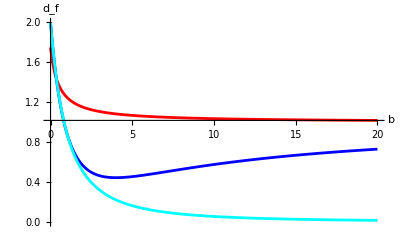

```mathematica
endRange=20;
dfRG2Lwf:=df;

plotSLE=Plot[dfSLE,{b,0,endRange},PlotStyle->Red,PlotRange->All];
plotRG2Lwf=Plot[dfRG2Lwf/.ϵ->2/.a->-2,{b,0,endRange},PlotStyle->Blue,PlotRange->All];
plotRG2L=Plot[dfRG2L/.ϵ->2,{b,0,endRange},PlotStyle->Cyan,PlotRange->All];
Show[{plotSLE,plotRG2Lwf,plotRG2L},PlotRange->{0,2},AxesLabel->{b,Subscript[d, f]}]
```

#### §§ 3d

```mathematica
Limit[dfRG2Lwf,b->∞]
%/.ϵ->1
%/.a->-2
```

1/8 (16-8 ϵ-a ϵ^2)

(8-a)/8

5/4

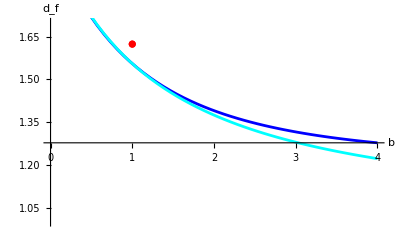

```mathematica
endRange=4;

Plot[dfRG2L/.ϵ->1,{b,0,endRange},PlotStyle->Blue,PlotRange->All];
plotRG2Lwf=Plot[dfRG2Lwf/.ϵ->1/.a->-2,{b,0,endRange},PlotStyle->Blue,PlotRange->All];
plotRG2L=Plot[dfRG2L/.ϵ->1,{b,0,endRange},PlotStyle->Cyan,PlotRange->All];

ListPlot[{{1,1.624}},PlotStyle->Red];

Show[{plotRG2Lwf,plotRG2L,%},PlotRange->{1,1.7},AxesLabel->{b,Subscript[d, f]}]
```

#### Extra data from my simulations

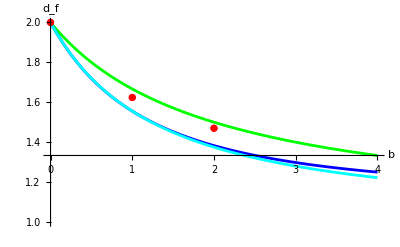

```mathematica
endRange=4;

plotRG1L=Plot[dfRG1L/.ϵ->1,{b,0,endRange},PlotStyle->Green,PlotRange->All];

plotRG2Lwf=Plot[dfRG2Lwf/.ϵ->1/.a->-1,{b,0,endRange},PlotStyle->Blue,PlotRange->All];
plotRG2L=Plot[dfRG2L/.ϵ->1,{b,0,endRange},PlotStyle->Cyan,PlotRange->All];

b0Simulation=ListPlot[{{0,2}},PlotStyle->Red];
b1Simulation=ListPlot[{{1,1.624}},PlotStyle->Red];
b2Simulation=ListPlot[{{2,1.47}},PlotStyle->Red];

Show[{plotRG1L,plotRG2Lwf,plotRG2L,b0Simulation,b1Simulation,b2Simulation},PlotRange->{1,2},AxesLabel->{b,Subscript[d, f]}]
```

### § With WF Also in U

```mathematica
dfRG1L:=2-b ϵ/(2+b)
dfRG2Lwf:=dfWF
dfRG2L:=2-b ϵ/(2+b)-b (ϵ/(2+b))^2
dfSLE=1+3/(4(2b+1));
```

#### §§ 2d

```mathematica
dfRG2Lwf
```

2-(b ϵ)/(2+b)+(b (a (-1+b)-4 (2+b)) ϵ^2)/(4 (2+b)^3)

Limits

b->∞

```mathematica
Limit[dfRG2Lwf,b->∞]
%/.ϵ->2
%/.a->-2
Limit[dfRG2L,b->∞]
%/.ϵ->2
```

1/4 (8-4 ϵ)

0

0

2-ϵ

0

b->0

```mathematica
Limit[dfRG2Lwf,b->0]
%/.ϵ->2
%/.a->-2
Limit[dfRG2L,b->0]
%/.ϵ->2
```

2

2

2

«2 more identical outputs»

Plots

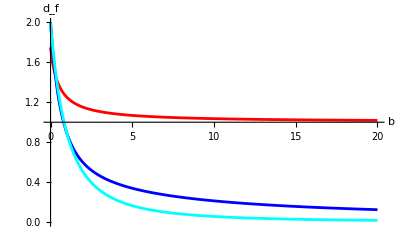

```mathematica
endRange=20;
dfRG2Lwf:=dfWF;

plotSLE=Plot[dfSLE,{b,0,endRange},PlotStyle->Red,PlotRange->All];
plotRG2Lwf=Plot[dfRG2Lwf/.ϵ->2/.a->+3,{b,0,endRange},PlotStyle->RGBColor[0, 0, 1],PlotRange->All];
plotRG2L=Plot[dfRG2L/.ϵ->2,{b,0,endRange},PlotStyle->RGBColor[0, 1, 1],PlotRange->All];
Show[{plotSLE,plotRG2Lwf,plotRG2L},PlotRange->{0,2},AxesLabel->{b,Subscript[d, f]},AxesOrigin->{0,1}]
```

```mathematica
(* It seems to go up, which is nice! *)
```

#### §§ 3d

Limits

b->∞

```mathematica
Limit[dfRG2Lwf,b->∞]
%/.ϵ->1
%/.a->-2

Limit[dfRG2L,b->∞]
%/.ϵ->1
```

1/4 (8-4 ϵ)

1

1

2-ϵ

1

b->0

```mathematica
Limit[dfRG2Lwf,b->0]
%/.ϵ->1
%/.a->-2

Limit[dfRG2L,b->0]
%/.ϵ->1
```

2

2

2

«2 more identical outputs»

Plots

#### Extra data from my simulations

```mathematica
dfRG2Lwf/.ϵ->1/.a->+3
```

2-b/(2+b)+(b (3 (-1+b)-4 (2+b)))/(4 (2+b)^3)

```mathematica
fitFunc
```

1.00096+0.5952/(2+b)^2+1.69664/(2+b)

```mathematica
fitFunc=Fit[{{0,2},{1,1.624},{2,1.47},{∞,1}},{1,1/(b+2),1/(b+2)^2},{b}];
```

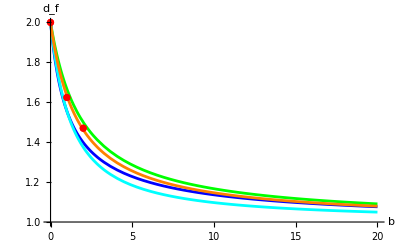

1.00096+0.5952/(2+b)^2+1.69664/(2+b)

```mathematica
inRange=0;
endRange=20;

plotRG1L=Plot[dfRG1L/.ϵ->1,{b,inRange,endRange},PlotStyle->RGBColor[0, 1, 0],PlotRange->All];

plotRG2Lwf=Plot[dfRG2Lwf/.ϵ->1/.a->+3,{b,inRange,endRange},PlotStyle->RGBColor[0, 0, 1],PlotRange->All];
plotRG2L=Plot[dfRG2L/.ϵ->1,{b,inRange,endRange},PlotStyle->RGBColor[0, 1, 1],PlotRange->All];

b0Simulation=ListPlot[{{0,2}},PlotStyle->Red];
b1Simulation=ListPlot[{{1,1.624}},PlotStyle->Red];
b2Simulation=ListPlot[{{2,1.47}},PlotStyle->Red];

fitPlot=Plot[fitFunc,{b,inRange,endRange},PlotStyle->Orange,PlotRange->All];

Show[{plotRG1L,plotRG2Lwf,plotRG2L,fitPlot,b0Simulation,b1Simulation,b2Simulation},PlotRange->{1,2},AxesLabel->{b,Subscript[d, f]},AxesOrigin->{0,1}]
```